## Test Systems

A collection of standard (and less standard systems)

### Smoothed Sprott Jerk systems from ??

```mathematica
Clear[Sprott,Di,Rd,Sa,Sg,He]
Sprott=<|
1-><|"fun" :>-a ypp+b yp-c y+d yp^2,"par"->{2.017,0,1,1,50},"IC"->{0,0,1}|>,2-><|"fun" :>a ypp-b yp+c y+d y^2,"par"->{0,2.8,1,1,50},"IC"->{-0.5,-1,1}|>,3-><|"fun" :>-a ypp-b yp+c y+d (y^2-1),"par"->{0.44,2,0,1,50},"IC"->{0,0,0}|>,4-><|"fun" :>-a ypp-b yp+c y+d y^2,"par"->{0.5,1,1,1,50},"IC"->{0,1,0}|>,5-><|"fun" :>a ypp-b yp+c y+d (Abs[y]-1),"par"->{0,2,0,1,50},"IC"->{-1,-1,1}|>,6-><|"fun" :>-a ypp-b yp+c y+d (Abs[y]-1),"par"->{0.6,1,0,1,50},"IC"->{0,0,0}|>,7-><|"fun" :>-a ypp-b yp+c y-d (Di[y]-1),"par"->{0.3,0.3,0,1,50},"IC"->{0,0,0}|>,8-><|"fun" :>-a ypp-b yp+c y-d (Rd[y]+1),"par"->{0.3,0.3,0,1,50},"IC"->{0,0,0}|>,9-><|"fun" :>a ypp-b yp+c y-d (Di[y]-1),"par"->{0,2.9,0.7,1,50},"IC"->{0,-0.5,0.5}|>,10-><|"fun" :>a ypp-b yp+c y-d (Rd[y]+1),"par"->{0,2.9,0.7,1,50},"IC"->{0,0.5,-0.5}|>,11-><|"fun" :>-a ypp-b yp-c y+d Sg[m][y],"par"->{0.5,1,1,1,50},"IC"->{0,1,0}|>,12-><|"fun" :>-a ypp-b yp+c y-d Sg[m][y],"par"->{0.5,1,1,1,50},"IC"->{0,1,0}|>,13-><|"fun" :>-a ypp-b yp-c y+d He[m][y],"par"->{0.7,1,1,1,50},"IC"->{0,1,0}|>,14-><|"fun" :>-a ypp-b yp-c y+d Sa[y],"par"->{0.4,1,1,2,50},"IC"->{0,1,0}|>,15-><|"fun" :>-a ypp-b yp+c y-d Sa[y],"par"->{0.4,1,1,2,50},"IC"->{0,1,0}|>,16-><|"fun" :>-a ypp-b yp-c y+d Tanh[y],"par"->{0.19,1,1,2,50},"IC"->{0,1,0}|>,17-><|"fun" :>-a ypp-b yp+c y-d Tanh[y],"par"->{0.19,1,1,2,50},"IC"->{0,1,0}|>,18-><|"fun" :>a ypp-b yp+c y-d y^3,"par"->{0,3.7,1,1,50},"IC"->{0,0.5,1}|>,19-><|"fun" :>-a ypp+b yp-c y-d yp^3,"par"->{0.6,2.8,1,1,50},"IC"->{0,1,0}|>,20-><|"fun" :>-a ypp-b yp+c y-d y^3,"par"->{0.7,1,1,1,50},"IC"->{0,1,0}|>,21-><|"fun" :>-a ypp-b yp-c y+d y^3,"par"->{0.35,1,1,1,50},"IC"->{0,1,0}|>,22-><|"fun" :>-a ypp-b yp+c y+d Sin[y],"par"->{0.2,1,0,1,50},"IC"->{0,1,0}|>|>;
(* Compute Derivtives automatically *)
NewSprott=Map[Function[entry,With[{der=D[entry["fun"],{{y,yp,ypp}}]},Append[entry,"der":>der]]],Sprott];
DerSub={Abs'[y]->Absp[y],Di'[y]->Dip[y],Rd'[y]->Rdp[y],Sa'[y]->Sap[y],Sg[m]'[y]->Sgp[m][y],He[m]'[y]->He[m][y]};
NewSprott=NewSprott/.DerSub
```

<|1→<|fun:>-a ypp+b yp-c y+d yp^2,par→{2.017,0,1,1,50},IC→{0,0,1},der:>{-c,b+2 d yp,-a}|>,2→<|fun:>a ypp-b yp+c y+d y^2,par→{0,2.8,1,1,50},IC→{-0.5,-1,1},der:>{c+2 d y,-b,a}|>,3→<|fun:>-a ypp-b yp+c y+d (y^2-1),par→{0.44,2,0,1,50},IC→{0,0,0},der:>{c+2 d y,-b,-a}|>,4→<|fun:>-a ypp-b yp+c y+d y^2,par→{0.5,1,1,1,50},IC→{0,1,0},der:>{c+2 d y,-b,-a}|>,5→<|fun:>a ypp-b yp+c y+d (Abs[y]-1),par→{0,2,0,1,50},IC→{-1,-1,1},der:>{c+d Absp[y],-b,a}|>,6→<|fun:>-a ypp-b yp+c y+d (Abs[y]-1),par→{0.6,1,0,1,50},IC→{0,0,0},der:>{c+d Absp[y],-b,-a}|>,7→<|fun:>-a ypp-b yp+c y-d (Di[y]-1),par→{0.3,0.3,0,1,50},IC→{0,0,0},der:>{c-d Dip[y],-b,-a}|>,8→<|fun:>-a ypp-b yp+c y-d (Rd[y]+1),par→{0.3,0.3,0,1,50},IC→{0,0,0},der:>{c-d Rdp[y],-b,-a}|>,9→<|fun:>a ypp-b yp+c y-d (Di[y]-1),par→{0,2.9,0.7,1,50},IC→{0,-0.5,0.5},der:>{c-d Dip[y],-b,a}|>,10→<|fun:>a ypp-b yp+c y-d (Rd[y]+1),par→{0,2.9,0.7,1,50},IC→{0,0.5,-0.5},der:>{c-d Rdp[y],-b,a}|>,11→<|fun:>-a ypp-b yp-c y+d Sg[m][y],par→{0.5,1,1,1,50},IC→{0,1,0},der:>{-c+d Sgp[m][y],-b,-a}|>,12→<|fun:>-a ypp-b yp+c y-d Sg[m][y],par→{0.5,1,1,1,50},IC→{0,1,0},der:>{c-d Sgp[m][y],-b,-a}|>,13→<|fun:>-a ypp-b yp-c y+d He[m][y],par→{0.7,1,1,1,50},IC→{0,1,0},der:>{-c+d He[m][y],-b,-a}|>,14→<|fun:>-a ypp-b yp-c y+d Sa[y],par→{0.4,1,1,2,50},IC→{0,1,0},der:>{-c+d Sap[y],-b,-a}|>,15→<|fun:>-a ypp-b yp+c y-d Sa[y],par→{0.4,1,1,2,50},IC→{0,1,0},der:>{c-d Sap[y],-b,-a}|>,16→<|fun:>-a ypp-b yp-c y+d Tanh[y],par→{0.19,1,1,2,50},IC→{0,1,0},der:>{-c+d Sech[y]^2,-b,-a}|>,17→<|fun:>-a ypp-b yp+c y-d Tanh[y],par→{0.19,1,1,2,50},IC→{0,1,0},der:>{c-d Sech[y]^2,-b,-a}|>,18→<|fun:>a ypp-b yp+c y-d y^3,par→{0,3.7,1,1,50},IC→{0,0.5,1},der:>{c-3 d y^2,-b,a}|>,19→<|fun:>-a ypp+b yp-c y-d yp^3,par→{0.6,2.8,1,1,50},IC→{0,1,0},der:>{-c,b-3 d yp^2,-a}|>,20→<|fun:>-a ypp-b yp+c y-d y^3,par→{0.7,1,1,1,50},IC→{0,1,0},der:>{c-3 d y^2,-b,-a}|>,21→<|fun:>-a ypp-b yp-c y+d y^3,par→{0.35,1,1,1,50},IC→{0,1,0},der:>{-c+3 d y^2,-b,-a}|>,22→<|fun:>-a ypp-b yp+c y+d Sin[y],par→{0.2,1,0,1,50},IC→{0,1,0},der:>{c+d Cos[y],-b,-a}|>|>

Define the defined  functions and their derivatives

```mathematica
Clear[Di,Dip,Rd,Rdp,Sa,Sap,Sg,Sgp,He,HEp,Absp,m]
Di[u_]:=Max[u,0]; Dip[u_]:=If[u>0,1,0]
Rd[u_]:=Min[u,0]; Rdp[u_]:=If[u<0,1,0]
Sa[u_]:=Piecewise[{ {-1, u<-1},{u, -1<u<1},{1,True}}]; Sap[u_]:=If[Abs[u]<1,1,0]
Sg[m_][u_]:=Tanh[m u]; Sgp[m_][u_]:=m Sech[m u]^2
He[m_][u_]:=(1+Tanh[m u])/2; Hep[m_][u_]:=1/2 m Sech[m u]^2
Absp[u_]:= If[u<0,-1,1]
```

### Rosseller and Lorenz Systems

```mathematica
ClearAll[Ross,dRoss,HRoss,dHRoss,Lor, dLor]
(* Rossler *)
(* {a,b,c} = {0.2,0.2,5.7} *)
Ross[{a_,b_,c_}][{x_,y_,z_}]:={-y-z,x+a y,b+z (x-c)}
dRoss[{a_,b_,c_}][{x_,y_,z_}]:={{0,-1,-1},{1,a,0},{z,0,x-c}}
(* Hyperchaotic Rossler *)
(* {a,b,c,d}={0.25,3,0.5,0.05} *)
HRoss[{a_,b_,c_,d_}][{x_,y_,z_,w_}]:={-y-z,x+a y+w,b+x z,-c z+d w}
dHRoss[{a_,b_,c_,d_}][{x_,y_,z_,w_}]:={{0,-1,-1,0},{1,a,0,1},{z,0,x,0},{0,0,-c,d}}
(*Lorenz*)
(* {sigma, rho, beta}={10,28,8/3} *)
Lor[{sigma_,rho_,beta_}][{x_,y_,z_}]:={sigma (y-x),x (rho-z)-y,x y-beta z};
dLor[{sigma_,rho_,beta_}][{x_,y_,z_}]:={{-sigma,sigma,0},{rho-z,-1,-x},{y,x,-beta}};
```

## Basic Solvers

Assume the systems are all defined by an autonomous ODE 
	y'=f(y) 
with f : ℝ^n → ℝ^n and a provided derivative df : ℝ^n → ℝ^(n×n) for the sensitivity computation
	J'=df(y).J

Our basic solver is going to simultaneously approximate 
	y'=f(y)  and J'=df(y).J
from an initial condition y(0)=y0 and J(0)=Id_n.  The solver returns a list containing interpolating functions for y and J

```mathematica
yJSolve[{f_,df_},y0_,TMax_]:=Module[{n=Length[y0],Id,y,J},
Id=IdentityMatrix[n];
 NDSolveValue[{
y'[t]==f[y[t]],y[0]==y0,
J'[t]==df[y[t]].J[t],J[0]==Id},{y,J},{t,0, TMax}]
]
```

Suggestions.

Tests

```mathematica
p={0.2,0.2,5.7};
y0={1,2,3}; TMax=123;
{ySol,JSol}=yJSolve[{Ross[p],dRoss[p]},y0,TMax]
ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All]
```

{InterpolatingFunction[{{0., 123.}}, <>],InterpolatingFunction[{{0., 123.}}, <>]}

-Graphics3D-

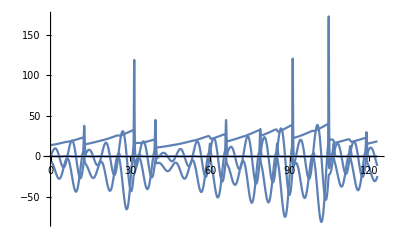

-Graphics3D-

```mathematica
p={0.25,3,0.5,0.05};
y0={-6.,0.,0.5,14.}; TMax=123;
{ySol,JSol}=yJSolve[{HRoss[p],dHRoss[p]},y0,TMax];
Plot[ySol[t],{t,0, TMax},PlotRange->All]
ParametricPlot3D[ySol[t]⟦{1,2,3}⟧,{t,0,TMax},PlotRange->All,PlotPoints->100]
```

Tests

## Poincare Sections

Restrict attention to hyperplane sections (p-p_0).n=0.
	In 2D this is a line perpendicular to the normal n through p_0.
	In 3D this is a plane perpendicular to the normal n through p_0.
	In 4D this is a hyperplane perpendicular to the normal n through p_0.
The advantage of a plane is that it is parameterized by a set of n-1 directions.  These tangent directions are perpendicular to the normal n. We can choose them to be orthogonal.

T is going to be an n×(n-1) matrix of the tangent vectors T=[t_1|t_2|…|t_(n-1)].  So Tᵀ.T=Id_(n-1) and Tᵀ.n=0_(n-1).  The section plane in all our codes is going to be described by the list
	{p0,n,T}
Switching n→-n gives the same hyperplane with the opposite orientation.

We want to compute a bunch of points on Poincare sections for various systems.  We want to ignore the transients and focus on the long term behaviour.

```mathematica
PoincarePoints[f_,{p0_,n_,T_},{TMin_, TMax_}]:=Module[{y},
Reap[ NDSolveValue[{y'[t]==f[y[t]],y[0]==y0,
WhenEvent[n.(y[t]-p0)>0,If[t>TMin, Sow[y[t]]]]},{y},{t,0, TMax}]]⟦2,1⟧
]
```

Test

```mathematica
{TMin,TMax}={12,123};
p={0.2,0.2,5.7}; y0={1,2,3};
{ySol,JSol}=yJSolve[{Ross[p],dRoss[p]},y0,TMax];
T=({{0, 0}, {1, 0}, {0, 1}});n={-1,0,0}; p0={5.7,0,0};
SecPts=PoincarePoints[Ross[p],{p0,n,T},{TMin,TMax}]
Show[
ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All],
ListPointPlot3D[SecPts,PlotStyle->Red]
]
```

{{5.7,2.1051,17.2246},{5.7,4.10909,6.72574},{5.7,3.63333,9.26099},{5.7,4.5413,3.82635},{5.7,1.96869,17.9574},{5.7,4.41035,4.89506},{5.7,2.59422,14.6353},{5.7,2.53148,0.405302},{5.7,2.47812,15.2448},{5.7,1.94222,0.322973},{5.7,2.88873,13.1015},{5.7,3.62798,0.735326},{5.7,1.56648,20.1475},{5.7,4.42602,1.63622},{5.7,1.0824,22.8435}}

-Graphics3D-

Lets test on the Hyper Chaos system.

```mathematica
p={0.25,3,0.5,0.05};
y0={-6.,0.,0.5,14.}; {TMin,TMax}={12,123};
{ySol,JSol}=yJSolve[{HRoss[p],dHRoss[p]},y0,TMax];
ParametricPlot3D[ySol[t]⟦{1,2,3}⟧,{t,0,TMax},PlotRange->All,PlotPoints->100,
AxesLabel->{"y_1","y_2","y_3"}]
```